```mathematica
Some computations for the revision of SPDE paper
By Le Chen.
Crated on Wed 19 Jan 2022 10:12:15 AM CST
```

```mathematica
f[n_]:=√(2 π n) (n/ⅇ)^n
```

```mathematica
FullSimplify[f[(k n)/2]^2/f[k n]//Expand,Assumptions->{k>=100,n>=200}]
```

2^(-1/2-k n) √(k n) √π

```mathematica
Limit[1/n Log[f[a n]/f[n]^a],n->∞,Assumptions->{a>0}]
```

a Log[a]

```mathematica
Limit[1/n Log[f[a n]/f[n]^a],n->Infinity,Assumptions->{a>0}]
```

a Log[a]

```mathematica
g[t_,x_]:=1/(√(2π t))Exp[-x^2/(2t)]
```

```mathematica
D[g[t,x],t]
```

-(ⅇ^(-x^2/(2 t)))/(2 √(2 π) t^(3/2))+(ⅇ^(-x^2/(2 t)) x^2)/(2 √(2 π) t^(5/2))

```mathematica
Integrate[D[g[t,x],t],{x,-∞,∞},Assumptions->t>0]
```

0

```mathematica
(Gamma[ a n+1]/Gamma[n+1]^a)^(1/n)
```

1/(2 t)

```mathematica
Integrate[(ⅇ^(-x^2/(2 t)) x^2)/(2 √(2 π) t^(5/2)),{x,-∞,∞},Assumptions->t>0]
```

1/(2 t)

```mathematica
D[g[t,x],x]
```

-(ⅇ^(-x^2/(2 t)) x)/(√(2 π) t^(3/2))

```mathematica
Integrate[(ⅇ^(-x^2/(2 t)) Abs[x])/(√(2 π) t^(3/2)),{x,-∞,∞},Assumptions->{5>t>0}]
```

```mathematica
(√(2/π))/(√t)(Gamma[ a n+1]/Gamma[n+1]^a)^(1/n)
```

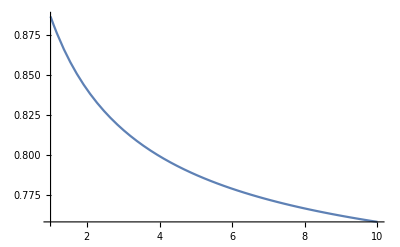

```mathematica
Limit[1/n Log[f[a n]/f[n]^a],n->∞,Assumptions->{a>0}]
```

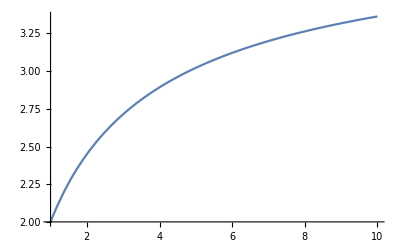

```mathematica
Plot[(Gamma[ a n+1]/Gamma[n+1]^a)^(1/n)/.a->2,{n,1,10}]
```

```mathematica
D[(Gamma[ a n+1]/Gamma[n+1]^a)^(1/n),n]//FullSimplify
```

-1/n^2(Gamma[1+n]^-a Gamma[1+a n])^(1/n) (a n (HarmonicNumber[n]-HarmonicNumber[a n])+Log[Gamma[1+n]^-a Gamma[1+a n]])